```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Get["../PlotStyles.m"]
```

/Users/yorickreum/PycharmProjects/pytorch_pde/approximator/examples/heat/results-thesis/hyperstudy-analysis

```mathematica
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
```

```mathematica
OverleafPath = "/Users/yorickreum/Dropbox/Apps/Overleaf/BA Thesis (MIT Template)"
```

/Users/yorickreum/Dropbox/Apps/Overleaf/BA Thesis (MIT Template)

```mathematica
(* dataRaw = Import["study_1598390958.csv", "Dataset", HeaderLines-> 1] *)
dataRaw = Import["study_1615752769_t_1615952223.518301.csv", "Dataset", HeaderLines-> 1]
```

False

```mathematica
DateDifference[DateObject["2021-03-13 05:08:01.659207"], DateObject["2021-03-17 00:19:39.842374"]]
```

3.79975 days

```mathematica
data = dataRaw[Select[(#"state" == "COMPLETE")&] , All][Select[(DateObject[#"datetime_complete"]- DateObject[#"datetime_start"]) > Quantity[1, "Minutes"]&],All][All,<|"Number" -> #"number", 
"Duration" -> QuantityMagnitude[
DateDifference[DateObject[#"datetime_start"],DateObject[#"datetime_complete"] ], "Seconds"],
"Hidden layers" -> #"params_n_hidden_layers",
"Neurons per layer" -> #"params_n_neurons_per_layer",
"Value" -> #"value"
|>&
]
```

```mathematica
KeyFlatten[as_Association]:=Association[Flatten[Map[Normal][KeyValueMap[List/*Replace[{{a_,b_Association}:>KeyMap[{a,#1}&,b],{a_,b_}:>Association[a->b]}]][as]]]]
KeyFlatten[l_List]:=l
KeyFlatten[a_/;AtomQ[a]]:=a
AssociationFlatten[as_Association]:=Map[KeyFlatten,as,{0,∞}]
AssociationSerialize=AssociationFlatten/*KeyValueMap[List/*Flatten]
```

AssociationFlatten/*KeyValueMap[List/*Flatten]

```mathematica
dataMedianized=<|"Hidden layers" -> #[[1]],"Neurons per layer" -> #[[2]],"Median value" -> #[[3]]|>& /@ data[ GroupBy["Hidden layers"],GroupBy["Neurons per layer"]][All,All,Merge[Median]][All,All,"Value"][AssociationSerialize];
```

```mathematica
dataMin=<|"Hidden layers" -> #[[1]],"Neurons per layer" -> #[[2]],"Minimal value" -> #[[3]]|>& /@ data[ GroupBy["Hidden layers"],GroupBy["Neurons per layer"]][All,All,Merge[Min]][All,All,"Value"][AssociationSerialize];
```

```mathematica
Total@Values@(Length/@ data[GroupBy["Hidden layers"],GroupBy["Neurons per layer"]][All,Keys])
```

40

```mathematica
First@SortBy[data, #Value&]
bestPts = {%["Hidden layers"], %["Neurons per layer"]}
```

{3,33}

```mathematica
First@dataMedianized[SortBy["Median value"]]
```

```mathematica
dataRaw[Select[#"number" == 424&],All]
```

```mathematica
data[Select[#"Value" == 0.00033867339381654437&],All]
```

```mathematica
Length@ptsPlt
```

387

```mathematica
ptsPlt = Normal@Values@data[All, {"Hidden layers", "Neurons per layer", "Value"}]
```

{{1,30,0.0000275737},{1,30,0.0000455505},{1,28,0.0000638292},{1,26,0.000986479},{1,30,0.0000240237},{1,30,0.000139363},{1,30,0.0000573437},{1,30,0.000325371},{1,30,0.000129573},{1,30,0.0000926193},{1,26,0.0000768921},{1,30,0.0000357929},{1,25,0.0000484863},{1,28,0.000393457},{1,26,0.0000132841},{1,30,0.0000190854},{1,30,0.0000652394},{1,26,0.000144365},{1,26,0.0000964199},{1,32,0.000021357},{1,30,0.000109015},{1,30,0.0000283432},{1,26,0.000397857},{1,30,0.0000589293},{1,26,0.0000116216},{1,26,0.0000239541},{1,30,0.000664104},{1,30,0.0000554133},{1,30,0.0000482801},{1,30,0.0000244117},{1,26,0.0000441863},{1,30,0.0000235125},{1,28,0.000237608},{1,30,0.000474522},{1,26,0.0000797286},{1,26,0.00192296},{1,30,0.0000251968},{1,26,0.0000593717},{1,30,7.63489×10^-6},{1,28,0.000398929},{1,28,0.0000279556},{1,26,0.000137853},{1,30,0.0000678061},{1,30,0.0000700448},{1,30,0.00108701},{1,30,0.000510875},{1,30,0.0000446474},{1,30,0.0000293735},{1,26,0.000371975},{1,30,0.000497944},{1,30,0.000634622},{1,30,0.0000132463},{1,30,0.000196687},{1,30,0.0000579199},{1,30,0.0000677702},{1,32,0.0000731354},{1,30,0.000236036},{1,30,0.0000292651},{1,30,0.0000536917},{1,30,0.0000133668},{1,30,0.0000351069},{1,32,0.000212679},{1,32,9.36946×10^-6},{2,32,7.34391×10^-6},{2,32,9.21641×10^-6},{2,32,0.0000122912},{2,32,8.0861×10^-6},{2,32,0.0000181092},{2,32,7.75325×10^-6},{2,32,8.91749×10^-6},{2,32,0.0000163328},{2,32,0.0000170127},{2,32,0.0000102793},{2,32,0.0000137209},{2,32,6.92915×10^-6},{2,33,0.0000102014},{2,33,0.0000111621},{2,32,0.0000114144},{2,32,0.0000140117},{2,32,8.94419×10^-6},{2,33,0.0000127337},{2,32,4.70267×10^-6},{2,32,0.0000115494},{2,32,9.70104×10^-6},{2,32,7.91587×10^-6},{2,32,0.000011647},{2,32,6.77934×10^-6},{2,32,0.0000134374},{2,32,0.0000102876},{2,32,8.87583×10^-6},{2,33,0.0000114861},{2,32,6.81793×10^-6},{2,32,8.11222×10^-6},{2,32,0.0000117552},{2,32,0.0000144152},{2,32,6.28587×10^-6},{2,32,7.78641×10^-6},{2,32,0.0000115714},{2,32,6.45469×10^-6},{2,32,6.59459×10^-6},{2,34,0.0000135823},{2,32,7.8086×10^-6},{2,32,5.76836×10^-6},{2,32,8.04872×10^-6},{2,32,0.0000126549},{2,32,8.32091×10^-6},{2,32,5.81383×10^-6},{2,32,0.0000167966},{2,33,0.0000116344},{2,32,6.7788×10^-6},{2,33,6.72222×10^-6},{3,35,6.66642×10^-6},{3,35,7.49815×10^-6},{3,35,8.79485×10^-6},{3,34,0.0000129431},{3,34,8.39071×10^-6},{3,33,9.04024×10^-6},{3,35,5.06336×10^-6},{3,35,0.0000112842},{3,35,0.0000103748},{3,35,9.65083×10^-6},{3,35,0.0000101795},{3,35,0.0000142218},{3,33,7.72113×10^-6},{3,34,7.46206×10^-6},{3,35,0.0000117847},{3,34,9.89256×10^-6},{3,34,5.7652×10^-6},{3,35,7.85819×10^-6},{3,34,8.52189×10^-6},{3,34,7.26443×10^-6},{3,35,6.52041×10^-6},{3,35,9.94664×10^-6},{3,35,9.80409×10^-6},{3,35,6.80116×10^-6},{3,35,0.0000154073},{3,35,7.81828×10^-6},{3,35,9.41864×10^-6},{3,34,0.0000274014},{3,35,7.97767×10^-6},{3,35,0.0000228608},{3,35,8.09979×10^-6},{3,35,9.63507×10^-6},{3,34,6.55491×10^-6},{3,35,7.30505×10^-6},{3,34,7.70327×10^-6},{3,34,7.32453×10^-6},{3,35,9.81814×10^-6},{3,35,6.28609×10^-6},{3,35,5.3581×10^-6},{3,36,9.1438×10^-6},{3,35,8.9715×10^-6},{3,36,7.57823×10^-6},{3,36,8.66145×10^-6},{3,35,0.0000106363},{3,36,5.29158×10^-6},{3,36,0.0000113512},{3,36,0.0000103883},{3,36,5.5791×10^-6},{3,34,7.73003×10^-6},{3,36,6.58188×10^-6},{3,36,8.33621×10^-6},{3,36,8.43569×10^-6},{4,36,0.228541},{4,36,9.33144×10^-6},{3,34,8.99874×10^-6},{4,36,7.37457×10^-6},{4,36,7.6428×10^-6},{4,36,9.00226×10^-6},{4,36,0.0000129029},{4,34,8.96367×10^-6},{4,37,0.0000128753},{4,36,6.84213×10^-6},{4,36,4.92072×10^-6},{4,36,0.0000105127},{4,36,5.66715×10^-6},{4,37,0.000010401},{4,36,6.84093×10^-6},{4,36,0.0000125082},{4,37,0.0000116572},{4,33,0.0000107434},{4,33,8.25661×10^-6},{4,34,6.6266×10^-6},{4,37,8.79699×10^-6},{4,33,5.34887×10^-6},{4,37,8.14238×10^-6},{4,37,0.0000109073},{4,37,0.0000110823},{4,37,8.08958×10^-6},{4,37,7.05281×10^-6},{4,37,6.91453×10^-6},{4,37,0.0000119125},{4,34,9.31718×10^-6},{4,37,7.63662×10^-6},{4,37,5.13135×10^-6},{3,37,9.08072×10^-6},{4,37,0.0000146302},{4,33,0.0000121746},{4,34,7.22956×10^-6},{4,37,6.79457×10^-6},{4,33,0.0000179589},{4,37,0.0000124899},{4,37,0.0000108611},{4,37,0.0000102218},{4,34,8.07211×10^-6},{4,37,0.0000100499},{4,34,7.02182×10^-6},{4,37,8.50362×10^-6},{4,37,0.0000144642},{5,37,9.36948×10^-6},{4,37,8.19103×10^-6},{4,37,0.228547},{4,33,4.92775×10^-6},{4,33,0.0000124285},{4,33,6.87094×10^-6},{4,37,0.00201575},{5,33,7.65726×10^-6},{2,31,9.67774×10^-6},{2,33,9.23458×10^-6},{5,38,8.35084×10^-6},{5,38,5.96555×10^-6},{5,31,0.0000121994},{2,38,0.000013641},{5,39,9.62925×10^-6},{2,38,0.0000104916},{2,31,7.31393×10^-6},{5,39,6.87613×10^-6},{5,31,9.70428×10^-6},{2,39,8.44098×10^-6},{5,31,9.05498×10^-6},{2,31,9.13216×10^-6},{2,39,0.0000135019},{5,40,8.95929×10^-6},{5,31,6.86996×10^-6},{5,31,7.32641×10^-6},{2,31,6.40602×10^-6},{5,31,9.78167×10^-6},{2,39,8.87684×10^-6},{5,34,6.77344×10^-6},{5,31,8.28067×10^-6},{5,31,8.61269×10^-6},{5,31,0.0000130859},{5,31,0.228541},{5,31,6.92692×10^-6},{5,34,7.25593×10^-6},{3,31,9.15316×10^-6},{5,31,7.76725×10^-6},{6,34,8.59167×10^-6},{5,34,6.25295×10^-6},{5,34,5.92061×10^-6},{18,34,0.0000272625},{12,34,0.0000306467},{3,34,9.32465×10^-6},{12,34,0.000030059},{3,40,0.0000118156},{6,34,7.30877×10^-6},{3,34,5.87622×10^-6},{6,34,0.22854},{6,34,5.10878×10^-6},{6,34,0.0000120794},{3,33,0.0000108524},{6,34,6.08382×10^-6},{6,33,0.228542},{3,33,8.01697×10^-6},{7,33,6.42264×10^-6},{6,33,8.1812×10^-6},{7,33,0.228541},{3,33,4.62898×10^-6},{7,33,0.0000110222},{6,33,0.0000121852},{6,35,6.07183×10^-6},{3,35,6.77335×10^-6},{6,35,0.0000829678},{6,33,0.0000120634},{6,33,7.21554×10^-6},{8,4,0.228542},{6,35,6.1293×10^-6},{6,35,9.25658×10^-6},{6,35,8.1321×10^-6},{6,35,8.11327×10^-6},{7,35,6.84662×10^-6},{7,36,0.0000162562},{7,36,0.0000101203},{7,36,9.44567×10^-6},{7,38,0.0000127862},{6,38,0.0000106935},{5,38,0.0000142216}}

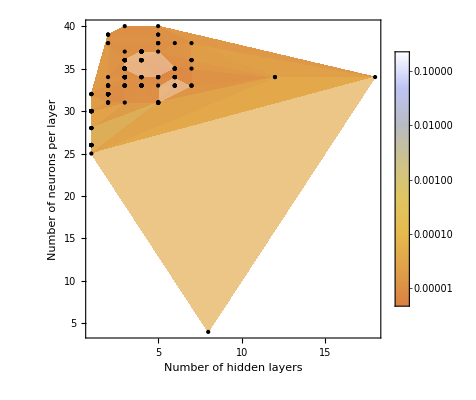

```mathematica
pltHyperparams = Show[
ListDensityPlot[
ptsPlt,
PlotRange->Full,
ClippingStyle->Automatic,
Mesh->Full,
Epilog->{
Style[Point[(#[[{1,2}]]&/@ ptsPlt)],Directive[Black]],
Style[Point[bestPts],Directive[Green]]
},
Mesh-> Full,
PlotTheme->"Detailed",
ScalingFunctions->"Log",
PlotRangePadding->Scaled[.01],
ColorFunction->"BeachColors",
PlotLegends->Placed[
BarLegend[Automatic,
LegendMarkerSize->340,
LegendMargins->{{10,0},{0,0}}],
Right]
],
FrameLabel-> {"Number of hidden layers","Number of neurons per layer"},
FrameStyle-> Black,
FrameTicks->{{LinTicks[1,40],None},{LinTicks[1,21],None}}
]
```

```mathematica
Export[FileNameJoin[{OverleafPath, "assets/figs/Evaluation/Heat/Hyperparameters-v2.pdf"}], pltHyperparams]
```

/Users/yorickreum/Dropbox/Apps/Overleaf/BA Thesis (MIT Template)/assets/figs/Evaluation/Heat/Hyperparameters-v2.pdf

```mathematica
UnitConvert[Quantity[Normal@data[{Min,Max},"Duration"], "Seconds"], "Hours"]
```

{0.593033 h,22.4562 h}

```mathematica
(DateObject /@ dataRaw[Select[(#"state" == "COMPLETE")&] , All][Select[(DateObject[#"datetime_complete"]- DateObject[#"datetime_start"]) > Quantity[1, "Minutes"]&],"datetime_start"])[{Min, Max}]
Differences@%
```

{3,33}

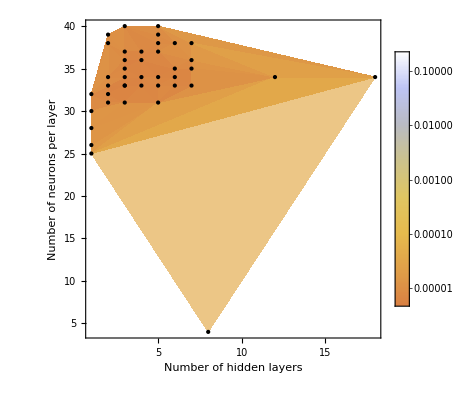

/Users/yorickreum/Dropbox/Apps/Overleaf/BA Thesis (MIT Template)/assets/figs/Evaluation/Heat/Hyperparameters-Min.pdf

```mathematica
ptsPlt = Normal@Values@dataMin[All, {"Hidden layers", "Neurons per layer", "Minimal value"}];
First@SortBy[%, #[[3]]&];
bestPts = %[[1;;2]]
pltHyperparams = Show[
ListDensityPlot[
ptsPlt,
PlotRange->Full,
ClippingStyle->Automatic,
Mesh->Full,
Epilog->{
Style[Point[(#[[{1,2}]]&/@ ptsPlt)],Directive[Black]],
Style[Point[bestPts],Directive[Green]]
},
Mesh-> Full,
PlotTheme->"Detailed",
ScalingFunctions->"Log",
PlotRangePadding->Scaled[.01],
ColorFunction->"BeachColors",
PlotLegends->Placed[
BarLegend[Automatic,
LegendMarkerSize->340,
LegendMargins->{{10,0},{0,0}}],
Right]
],
FrameLabel-> {"Number of hidden layers","Number of neurons per layer"},
FrameStyle-> Directive[Black,13],
FrameTicks->{{LinTicks[1,40],None},{LinTicks[1,21],None}}
]
Export[FileNameJoin[{OverleafPath, "assets/figs/Evaluation/Heat/Hyperparameters-Min.pdf"}], pltHyperparams]
```

{5,34}

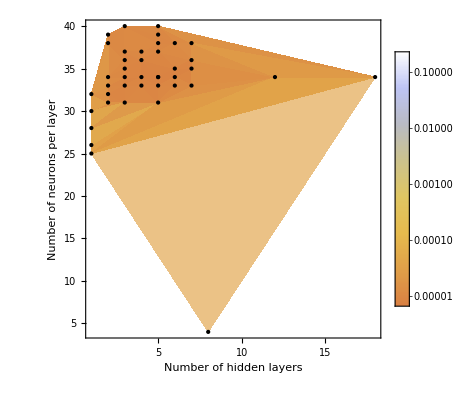

/Users/yorickreum/Dropbox/Apps/Overleaf/BA Thesis (MIT Template)/assets/figs/Evaluation/Heat/Hyperparameters-Median.pdf

```mathematica
ptsPlt = Normal@Values@dataMedianized[All, {"Hidden layers", "Neurons per layer", "Median value"}];
First@SortBy[%, #[[3]]&];
bestPts = %[[1;;2]]
pltHyperparams = Show[
ListDensityPlot[
ptsPlt,
PlotRange->Full,
ClippingStyle->Automatic,
Mesh->Full,
Epilog->{
Style[Point[(#[[{1,2}]]&/@ ptsPlt)],Directive[Black]],
Style[Point[bestPts],Directive[Green]]
},
Mesh-> Full,
PlotTheme->"Detailed",
ScalingFunctions->"Log",
PlotRangePadding->Scaled[.01],
ColorFunction->"BeachColors",
PlotLegends->Placed[
BarLegend[Automatic,
LegendMarkerSize->340,
LegendMargins->{{10,0},{0,0}}],
Right]
],
FrameLabel-> {"Number of hidden layers","Number of neurons per layer"},
FrameStyle-> Directive[Black,13],
FrameTicks->{{LinTicks[1,40],None},{LinTicks[1,21],None}}
]
Export[FileNameJoin[{OverleafPath, "assets/figs/Evaluation/Heat/Hyperparameters-Median.pdf"}], pltHyperparams]
```